Pumping power is -10.11dBm.

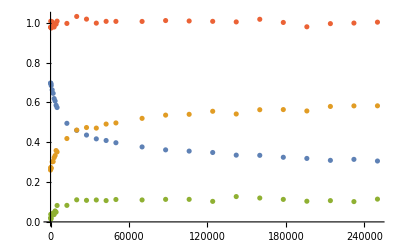

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"optimal_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 5.dBm.

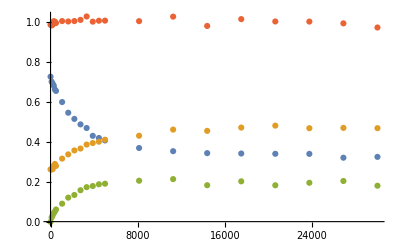

```mathematica
file=path<>"high_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is -25.dBm.

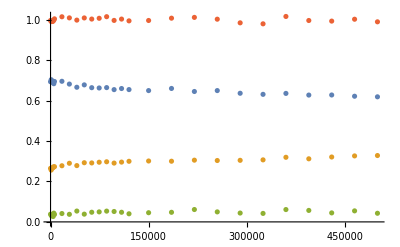

```mathematica
file=path<>"low_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

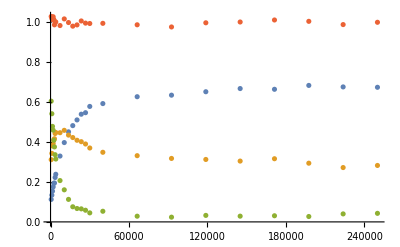

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```